In this notebook we derive some of the mathematical tools we used to analyze the adaptive dynamics of our model. In particular, we derive explicit expressions for invasion fitness, for the selection gradient and for the curvature of the fitness function. Other derivations are presented in the manuscript.

The model

The model is as follows:

```mathematica
(* Transition matrix *)
Λ=S.M.R;

(* Survival matrix *)
S=({{Subscript[s, 1], 0}, {0, Subscript[s, 2]}});

(* Migration matrix *)
M=({{1-m, m}, {m, 1-m}});

(* Reproduction matrix *)
R=({{Subscript[r, 1], 0}, {0, Subscript[r, 2]}});

(* Reproduction function *)
Subscript[r, 1][x_]:=Piecewise[{{Subscript[r, max],Subscript[w, 1][x]>c Subscript[r, max]},{Subscript[w, 1][x]/c,Subscript[w, 1][x]>0}},0];
Subscript[r, 2][x_]:=Piecewise[{{Subscript[r, max],Subscript[w, 2][x]>c Subscript[r, max]},{Subscript[w, 2][x]/c,Subscript[w, 2][x]>0}},0];

(* Survival function *)
Subscript[s, 1][x_]:=1/(1+Exp[-a Subscript[w, 1][x]]);
Subscript[s, 2][x_]:=1/(1+Exp[-a Subscript[w, 2][x]]);

(* Water surplus *)
Subscript[w, 1][x_]:=Subscript[W, 1]/Subscript[n, 1]-x;
Subscript[w, 2][x_]:=Subscript[W, 2]/Subscript[n, 2]-x;
```

#### Population dynamics

Here we have a look at what the population dynamics of our model look like under a fixed set of parameters, e.g.

```mathematica
(* Example parameter set *)
pars={m->0.5,Subscript[W, 1]->600,Subscript[W, 2]->100,c->1,a->5,Subscript[r, max]->3};
```

We then evaluate the population densities in the two patches at various time steps given a trait value and some initial conditions.

```mathematica
(* Rule to make the equations explicit *)
expl={Subscript[s, 1]->Subscript[s, 1][x],Subscript[s, 2]->Subscript[s, 2][x],Subscript[r, 1]->Subscript[r, 1][x],Subscript[r, 2]->Subscript[r, 2][x]};

(* Equations describing the dynamics *)
eq={Subscript[n, 1][t+1],Subscript[n, 2][t+1]}==(Λ/.expl/.{Subscript[n, 1]->Subscript[n, 1][t],Subscript[n, 2]->Subscript[n, 2][t]}).{Subscript[n, 1][t],Subscript[n, 2][t]}/.pars/.x->3;

(* Initial conditions *)
init={Subscript[n, 1][0]==1,Subscript[n, 2][0]==1};
```

Now evaluate.

```mathematica
(* Numerical evaluation *)
tab=RecurrenceTable[{eq,init},{Subscript[n, 1],Subscript[n, 2]},{t,0,49}];
```

And plot.

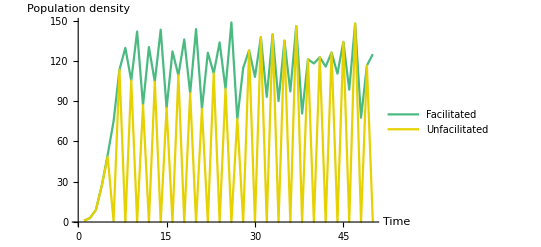

```mathematica
(* Plotting *)
ListLinePlot[Transpose[tab],PlotStyle->{RGBColor[0.29,0.73,0.5],RGBColor[0.9,0.82,0.01]},PlotRange->Full,PlotLegends->{"Facilitated","Unfacilitated"},AxesLabel->{"Time","Population density"}]
```

### Invasion fitness

Next, we compute the invasion fitness of the mutant as the leading eigenvalue of the transition matrix.

```mathematica
λ=Λ//Eigenvalues//Last
```

1/2 (p_1 q_1-m p_1 q_1+p_2 q_2-m p_2 q_2+√((-p_1 q_1+m p_1 q_1-p_2 q_2+m p_2 q_2)^2-4 (p_1 p_2 q_1 q_2-2 m p_1 p_2 q_1 q_2)))

We now check that the invasion fitness is indeed one when evaluated at the resident, i.e. when the mutant is the resident, under a random set of parameter values.

```mathematica
(* Example parameter set *)
pars={m->0.5,Subscript[k, 1]->5000,Subscript[k, 2]->5000,Subscript[r, max]->2,s->0.3,a->5,Subscript[θ, 1]->0,Subscript[θ, 2]->4};
```

For this we need to find the equilibrium population densities given the parameters (we do that numerically).

```mathematica
(* Find equilibrium densities *)
eq={Subscript[n, 1],Subscript[n, 2]}==Λ.{Subscript[n, 1],Subscript[n, 2]}/.Subscript[p, 1]->p[x,Subscript[θ, 1]]/.Subscript[p, 2]->p[x,Subscript[θ, 2]]/.Subscript[q, 1]->Subscript[q, 1][x]/.Subscript[q, 2]->Subscript[q, 2][x];
sol=FindRoot[eq/.pars/.x->4,{{Subscript[n, 1],5000},{Subscript[n, 2],5000}}]
```

{n_1→3927.27,n_2→1963.63}

Then, we plug those equilibrium densities into the invasion fitness function, with the rest of the parameters.

```mathematica
(* Invasion fitness of the resident *)
λ/.Subscript[p, 1]->p[x,Subscript[θ, 1]]/.Subscript[p, 2]->p[x,Subscript[θ, 2]]/.Subscript[q, 1]->Subscript[q, 1][x]/.Subscript[q, 2]->Subscript[q, 2][x]/.pars/.sol/.x->4
```

1.

Now that we have the invasion fitness, we want to get a formula for the selection gradient, which will help us identify singular strategies and long-term evolutionary equilibria.

### Selection gradient (not used just yet)

We know that the selection gradient can be expressed in terms of the derivative of the transition matrix (here dΛ) and the left and right dominant eigenvectors (v and u, respectively) of said matrix (Otto and Day), as such:

```mathematica
(* Selection gradient *)
G=v.dΛ.u/(v.u);
```

which we can express in terms of the derivatives of the fitness function in each patch, w_1 and w_2, respectively,

```mathematica
dΛ=M.dQ;
dQ=({{Subscript[dw, 1], 0}, {0, Subscript[dw, 2]}});
Subscript[w, 1][x_]:=w[x,θ1,Subscript[n, 1],k1];
Subscript[w, 2][x_]:=w[x,θ2,Subscript[n, 2],k2];
```

We can now identify (and rescale) a pair of possible left and right eigenvectors for the transition matrix:

```mathematica
(* Left and right eigenvectors *)
left=(Λ//Eigenvectors//Last) m Subscript[w, 1]
right=(Λ//Transpose//Eigenvectors//Last) m Subscript[w, 2]
```

{1/2 (w_1-m w_1-w_2+m w_2+√(w_1^2-2 m w_1^2+m^2 w_1^2-2 w_1 w_2+4 m w_1 w_2+2 m^2 w_1 w_2+w_2^2-2 m w_2^2+m^2 w_2^2)),m w_1}

{1/2 (w_1-m w_1-w_2+m w_2+√(w_1^2-2 m w_1^2+m^2 w_1^2-2 w_1 w_2+4 m w_1 w_2+2 m^2 w_1 w_2+w_2^2-2 m w_2^2+m^2 w_2^2)),m w_2}

It looks like the eigenvectors can be rewritten in terms of λ:

```mathematica
λ-(1-m)Subscript[w, 2]==left[[1]]==right[[1]]//Simplify
```

True

Hence, we can rewrite more simply them as:

```mathematica
(* Re-write the eigenvectors *)
left[[1]]=λ-(1-m)Subscript[w, 2];
right[[1]]=λ-(1-m)Subscript[w, 2];
```

We can now get an expression for the selection gradient by substituting those in the previous formula, and evaluating the result at the resident (i.e. when λ = 1).

```mathematica
G=G/.u->left/.v->right/.λ->1//Simplify
```

(m^2 dw_2 w_1+dw_1 (1-m-(2-4 m+m^2) w_2+(1-3 m+2 m^2) w_2^2))/(1+(-2+2 m+m^2 w_1) w_2+(-1+m)^2 w_2^2)

We could also have obtained a selection gradient by differentiating the invasion fitness function directly, but this would take a lot of computation time, especially if (as we shall see) we have to repeat this numerically for many possible combinations of parameters. That said, we can compare the expression we just derived to that more “brute-force” approach, to make sure our selection gradient is correct, given the same parameter values (and demographic equilibria) we have tried before.

```mathematica
(* Differentiate the invasion fitness *)
diff=D[λ/.{Subscript[w, 1]->Subscript[w, 1][x],Subscript[w, 2]->Subscript[w, 2][x]},x];

(* Evaluate at resident *)
diff/.y->x/.pars/.neq/.x->3
```

1.1878

Now we compute the derivatives of w_1 and w_2 to be able to evaluate the formula for the fitness gradient.

```mathematica
Subscript[dw, 1][x_]:=D[Subscript[w, 1][y],y]/.y->x;
Subscript[dw, 2][x_]:=D[Subscript[w, 2][y],y]/.y->x;
G/.Subscript[w, 1]->Subscript[w, 1][x]/.Subscript[w, 2]->Subscript[w, 2][x]/.Subscript[dw, 1]->Subscript[dw, 1][x]/.Subscript[dw, 2]->Subscript[dw, 2][x]/.pars/.neq/.x->3
```

1.1878

### Singular strategies

There may be values of trait x for which the selection gradient becomes zero. Those are termed evolutionary singular strategies, evolutionary steady-states or evolutionary equilibria. We could not find such values analytically because the value of the selection gradient at a given trait value depends on the equilibrium size of the population given that trait value, and there is no explicit expression for that (above we had to find the demographic equilibrium through numerical root finding). Hence, here we solved for the roots of the selection gradient numerically, under various sets of parameters. We did this elsewhere, as this notebook is primarily about showing the derivations of the mathematical expressions we used.

### Evolutionary stability

Once a singular strategy has been found, it is not guaranteed that this is an endpoint of evolution. For this, the singularity must be evolutionarily stable, that is, once the population is there, it does not evolve away. Mathematically, this happens when the second derivative of the invasion fitness with respect to the mutant trait value is negative when evaluated at the singularity. So, the criterion for evolutionary stability (or invasion-proofness) involves the curvature of the invasion fitness function. It can be shown (see Appendix) that this curvature, when evaluated at a singular strategy, is

```mathematica
(* Fitness curvature *)
F=(dv.dΛ.u+v.ddΛ.u+v.dΛ.du)/(v.u);
```

where d symbolizes a derivative and dd symbolizes the second derivative (of the transition matrix in the case of ddΛ).

We can show that at equilibrium, the derivatives of vectors u and v are

```mathematica
(* Derivatives of the eigenvectors *)
dleft={(m-1)Subscript[dw, 2],m Subscript[dw, 2]};
dright={(m-1)Subscript[dw, 2],m Subscript[dw, 1]};
```

We can also express the second derivative of the transition matrix in terms of the second derivatives of w_1 and w_2, as such:

```mathematica
(* Second derivative of the transition matrix *)
ddΛ=M.ddQ;
ddQ=({{Subscript[ddw, 1], 0}, {0, Subscript[ddw, 2]}});
Subscript[ddw, 1][x_]:=D[D[Subscript[w, 1][y],y],y]/.y->x;
Subscript[ddw, 2][x_]:=D[D[Subscript[w, 2][y],y],y]/.y->x;
```

Now we can substitute the above into the expression for the fitness curvature at equilibrium, and simplify, which gives us

```mathematica
F/.u->left/.v->right/.du->dleft/.dv->dright/.λ->1//Simplify
```

(m^2 (ddw_2 w_1+dw_2^2 (1+(-1+m) w_1))+m^2 dw_1^2 (1+(-1+m) w_2)-(-1+m) dw_1 dw_2 (2 (-1+m)+m^2 w_1+(2-4 m+m^2) w_2)+ddw_1 (1-m-(2-4 m+m^2) w_2+(1-3 m+2 m^2) w_2^2))/(1+(-2+2 m+m^2 w_1) w_2+(-1+m)^2 w_2^2)

As for the selection gradient above, we could check the validity of this formula by comparing it to brute-force second-differentiation of the invasion fitness, but we need to do it at a singular strategy, that is, when the selection gradient is zero. This means that we first have to find one potential such equilibrium.

Again, the selection gradient depends on equilibrium population sizes, and there is no explicit expression for those, so we could not solve the root of the selection gradient analytically. Instead, we numerically solved a system of equations to find the combination of x and population sizes that simultaneously solve both the demographic equilibrium (population does not change size anymore) and the evolutionary equilibrium (selection gradient is zero).  We did this as follows:

```mathematica
(* System of equations to solve *)
eqs={{Subscript[n, 1],Subscript[n, 2]}==Λ. {Subscript[n, 1],Subscript[n, 2]},G==0}/.Subscript[dw, 1]->Subscript[dw, 1][x]/.Subscript[dw, 2]->Subscript[dw, 2][x]/.Subscript[w, 1]->Subscript[w, 1][x]/.Subscript[w, 2]->Subscript[w, 2][x];

(* Solve numerically *)
neq=FindRoot[eqs/.pars,{{Subscript[n, 1],10000},{Subscript[n, 2],10000},{x,100}}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {n_1,n_2,x} = {2.44276,2.44276,14799.8}. Try perturbing the initial point(s).

{n_1→2.44276,n_2→2.44276,x→14799.8}

Now that we have a candidate singular strategy, we can double-differentiate the invasion fitness function from scratch to get an expression for the curvature, and evaluate it at the singularity.

```mathematica
(* Brute-force differentiation *)
diff2=D[diff,x];

(* Evaluate at equilibrium *)
diff2/.pars/.neq
```

-2.45458×10^-16

We can now compare that value with that obtained from our derived formula for the curvature:

```mathematica
F/.dv->dright/.du->dleft/.v->right/.u->left/.Subscript[ddw, 1]->Subscript[ddw, 1][x]/.Subscript[ddw, 2]->Subscript[ddw, 2][x]/.Subscript[dw, 1]->Subscript[dw, 1][x]/.Subscript[dw, 2]->Subscript[dw, 2][x]/.Subscript[w, 1]->Subscript[w, 1][x]/.Subscript[w, 2]->Subscript[w, 2][x]/.pars/.neq
```

-2.45458×10^-16

(Those should be the same.)

### Convergence stability

We just derived an expression for the curvature of the invasion fitness function, which allows us to evaluate whether a given singularity (trait value such that the selection gradient is zero) is evolutionarily stable, or invasion-proof. However, evolutionary stability only means that a trait value will stay where it is once the population is at the singularity, but it does not say whether evolution will lead to that singularity in the first place. Whether a singular strategy is attainable has to do with convergence stability, and for a singular strategy to be convergence-stable, the requirement is that the selection gradient is negative for trait values that are above the singularity, and positive for trait values that are below the singularity (i.e. the selection gradient leads towards the singularity). Mathematically, this means that the derivative of the selection gradient with respect to the resident strategy must be negative when evaluated at the singular point. This is different from the curvature of the fitness function, which is the second derivative of the invasion fitness with respect to the mutant, which is then evaluated at the singularity. As we explain in the manuscript, we could not come up with an explicit expression for the derivative of the selection gradient with respect to the resident trait value, because as the resident trait value changes the demographic equilibrium also changes, such that differentiating the selection gradient requires involves the derivatives of those equilibrium population sizes, for which we do not have an explicit expression. Hence, for all intents and purposes we used numerical evaluation of the selection gradient around singularities to estimate whether said singularity was convergence-stable.